```mathematica
c   = 3 10^8;
τ = 30 10^-9;
λ = 670 10^-9;
ω = 2 π c/λ;
ωr = 10^8;
ω =N[ ω τ];
ωr = N[ωr τ];
```

0.480434

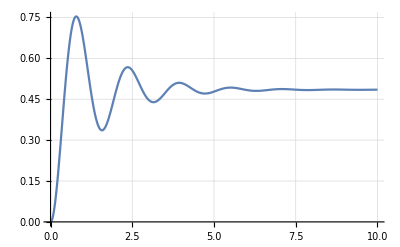

```mathematica
ω = 0;
ωr = 2;
eqs = {
D[x[t], t] == y[t]+2 Cos[t ω] z[t] ωr,
D[y[t], t] == -y[t]-2 Cos[t ω] z[t] ωr,
D[z[t], t] == -z[t]/2-Cos[t ω] x[t] ωr+Cos[t ω] y[t] ωr,
x[0] == 1, y[0] == 0, z[0] == 0
};
tMax = 10;
{xS, yS, zS} = NDSolveValue[eqs, {x, y, z}, {t, 0, tMax},MaxSteps->2 10^7];
Integrate[yS[t], {t, 0, tMax}]/tMax
Plot[yS[t], {t, 0, tMax}, PlotRange->Full, GridLines->Automatic]
```

```mathematica
ParametricPlot3D[{10(xS[t]-1), 22 yS[t], zS[t]}, {t, 0, tMax}]
```